```mathematica
σ=2/10;ρ=1/10;r=3/100;
Σ[i_]:=σ;Π[i_,j_]:=Piecewise[{{1, i==j}, {ρ, True}}];
n=3;
σI=Sqrt[ Sum[Σ[i]Σ[j]Π[i,j],{i,n},{j,n}]]/n//N
qI=1/n Sum[1/2Σ[i]^2,{i,n}]-1/2 σI^2//N
I0=Product[100,{i,n}]^(1/n);
```

0.126491

0.012

```mathematica
Timing[
InputForm[FinancialDerivative[{"American","Put"}, {"StrikePrice"-> 100, "Expiration"->1/4},  {"InterestRate"-> r, "Volatility" ->σI, "CurrentPrice"-> I0, "Dividend"->qI},"GridSize"->{2^16,7000}]]
]
```

{71.261,2.3271362219357212}

```mathematica
(*no strang 200*)
100(2.32625975468735/2.325976-1)
```

0.0121994

```mathematica
(*strang 110*)
100(2.32577169859819/2.325976-1)
```

-0.00878347

```mathematica
(*no strang 366*)
100(2.32614310359909/2.325976-1)
```

0.00718424

```mathematica
(*strang 200*)
100(2.32587716544954/2.325976-1)
```

-0.00424916

```mathematica
InputForm[FinancialDerivative[{"American","Put"}, {"StrikePrice"-> 100, "Expiration"->1/4},  {"InterestRate"-> r, "Volatility" ->σI, "CurrentPrice"-> I0, "Dividend"->qI},"GridSize"->{2^16,2500}]]
```

3.004451843936393

```mathematica
FinancialDerivative[{"American","Put"}, {"StrikePrice"-> 100.00, "Expiration"->0.25},  {"InterestRate"-> r-qI, "Volatility" ->σI, "CurrentPrice"-> I0, "Dividend"->0},"GridSize"->{2^10,10000}]
```

2.91137

```mathematica
l=Transpose[Table[FinancialDerivative[{"American","Put"}, {"StrikePrice"-> 100.00, "Expiration"->0.25},  {"InterestRate"-> r, "Volatility" ->σI, "CurrentPrice"-> I0, "Dividend"->qI},"GridSize"->{2^i,j}],{i,15,16},{j,1000,5000,1000}]];
```

```mathematica
Log[Abs[1-l/2.90980]]/Log[10]//MatrixForm
```

(-4.58559 | -4.59752
-4.86154 | -4.8847
-5.01534 | -5.04865
-5.11871 | -5.16204
-5.19533 | -5.24777)

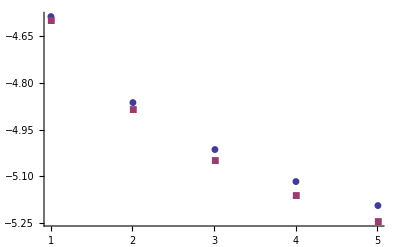

```mathematica
ListPlot[Log[Abs[1-Transpose[l]/2.90980]]/Log[10],PlotRange->All,PlotMarkers->Automatic]
```

```mathematica
l[[5,2]]
```

2.90978

```mathematica
InputForm[l]
```

{11.73403343452288, 2.3549295950617433, 3.3524689555958487, 3.2045800655244165, 
 3.25412776516467, 3.2458267025112217, 3.2604939057014337, 3.261751509328421, 
 3.262145887167553}

```mathematica
Expand[(Sum[dS[j]D[ga,S[j]],{j,nn}]+1/2Sum[dS[j]dS[k]D[ga,S[j],S[k]],{j,5},{k,nn}])/ga]
```

-dS[1]^2/(9 S[1]^2)+dS[1]/(3 S[1])-dS[2]^2/(9 S[2]^2)+dS[2]/(3 S[2])+(dS[1] dS[2])/(9 S[1] S[2])-dS[3]^2/(9 S[3]^2)+dS[3]/(3 S[3])+(dS[1] dS[3])/(9 S[1] S[3])+(dS[2] dS[3])/(9 S[2] S[3])

```mathematica
D[ga,S[1],S[1]]
```

-(2 S[2]^(1/3) S[3]^(1/3))/(9 S[1]^(5/3))

```mathematica
Exit[]
```

```mathematica
nn=3;
ga:=Product[S[i]^(1/nn),{i,nn}];
Σ[i_]:=σ[i];Π[i_,j_]:=Piecewise[{{1, i==j}, {ρ[i,j], i<j}, {ρ[j,i], i>j}}]
repla=Prepend[Join[Table[dW[i]dt->0,{i,nn}],Flatten[Table[dW[i]dW[j]->dt Π[i,j],{j,nn},{i,j}]]],dt^2-> 0];
dS[i_]:=S[i](r dt+Σ[i]dW[i]);
σI=Sqrt[Sum[Σ[i]Σ[j]Π[i,j],{i,nn},{j,nn}]]/nn;
qI=3/2Sum[Σ[i]^2,{i,nn}]/nn^2-σI^2/2;
```

```mathematica
(* d(ga)/ga *)
```

```mathematica
Collect[Expand[(Sum[dS[j]D[ga,S[j]],{j,nn}]+1/2Sum[dS[j]dS[k]D[ga,S[j],S[k]],{j,5},{k,nn}])/ga]/.repla,dt]
```

1/3 dW[1] σ[1]+1/3 dW[2] σ[2]+1/3 dW[3] σ[3]+dt (r-σ[1]^2/9+1/9 ρ[1,2] σ[1] σ[2]-σ[2]^2/9+1/9 ρ[1,3] σ[1] σ[3]+1/9 ρ[2,3] σ[2] σ[3]-σ[3]^2/9)

```mathematica
(*test*)
Simplify[(Expand[(1/3 dW[1] σ[1]+1/3 dW[2] σ[2]+1/3 dW[3] σ[3])^2]/.repla)-σI^2 dt]
```

0

```mathematica
(* qI *)
qI=-(-σ[1]^2/9+1/9 ρ[1,2] σ[1] σ[2]-σ[2]^2/9+1/9 ρ[1,3] σ[1] σ[3]+1/9 ρ[3] σ[2] σ[3]-σ[3]^2/9)
```

σ[1]^2/9-1/9 ρ[1,2] σ[1] σ[2]+σ[2]^2/9-1/9 ρ[1,3] σ[1] σ[3]-1/9 ρ[2,3] σ[2] σ[3]+σ[3]^2/9